## Vtotal integrands

```mathematica
Vtot=ηc
π
−π
1
a
(L/2)+σf
−(L/2)+σf
(r^ 2)δ(−AO (ρ^(−6))+BO(ρ^(−12))) dz

+

(L/2)
−(L/2)
(r^ 2)δ(−AC(ρ^(−6))+BC(ρ^(−12))) dz

+

(L/2)−σf
−(L/2)−σf
(r^2)δ(−AO (ρ^(−6))+BO (ρ^(−12))) dz

dδ dθ
```

## Vtot integrand only for one particle case

```mathematica
ηc

1
a
(L/2)
−(L/2)
π
−π
(r^2)δ(−A(ρ^(−6))+B(ρ^(−12))) dδ dzdθ
```

## LJ Potential function (important)

```mathematica
Subρ=Sqrt[(r^2)(δ^2)+(z−z0)^2]
Subρ
```

√((z-z0)^2+r^2 δ^2)

√((z-z0)^2+r^2 δ^2)

```mathematica
SubA=4ϵ σ^6
SubB=4ϵ σ^12
```

4 ϵ σ^6

4 ϵ σ^12

```mathematica
Phi[ρ]=(r^2)δ(−A(ρ^(−6))+B(ρ^(−12)))/.{A->SubA,B->SubB,ρ->Subρ}
```

r^2 δ (-(4 ϵ σ^6)/(((z-z0)^2+r^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+r^2 δ^2)^6))

## Trying to integrate the function over bounds for one particle

First of all the integral below is what I think the paper meant to show, but it doesn’t run.

```mathematica
Integrate[r^2 δ (-(4 ϵ σ^6)/(((z-z0)^2+r^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+r^2 δ^2)^6)),{δ,.25,1},{z,-(L/2),(L/2)},{θ,-pi,pi}]
```

I don’t know which of the bounds (-pi to pi and a to 1) apply to which variable (lambda and theta).

Integral result if a,1 bounds are for theta and not lambda. Symbolic result in terms of lambda.

```mathematica
Integrate[Phi[ρ],{z,-(L/2),(L/2)},{θ,a,1}]
```

ConditionalExpression[-4 (-1+a) r^2 δ ϵ σ^6 (1/(1280 r^11 δ^11)((65536 r^9 (L-2 z0) δ^9 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^5)+(18432 r^7 (L-2 z0) δ^7 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^4)+(5376 r^5 (L-2 z0) δ^5 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^3)-(80 r^3 (L-2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^2)-(30 r (L-2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2-4 L z0+4 (z0^2+r^2 δ^2))-15 (32 r^6 δ^6-21 σ^6) ArcTan[(L-2 z0)/(2 r δ)])-1/(1280 r^11 δ^11)(-(65536 r^9 (L+2 z0) δ^9 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^5)-(18432 r^7 (L+2 z0) δ^7 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^4)-(5376 r^5 (L+2 z0) δ^5 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^3)+(80 r^3 (L+2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^2)+(30 r (L+2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2+4 L z0+4 (z0^2+r^2 δ^2))+15 (32 r^6 δ^6-21 σ^6) ArcTan[(L+2 z0)/(2 r δ)])), ]

NIntegrate using -pi to pi for lambda but it diverges (accidentally used 0,1 for theta instead of a,1 but either way it diverges).

```mathematica
NIntegrate[Phi[ρ],{δ,-pi,pi},{z,-(L/2),(L/2)},{θ,0,1}]
```

NIntegrate::nlim: δ = pi is not a valid limit of integration.

NIntegrate::oidiv: The odd integrand Phi[ρ] is being considered as zero over the specified region, but may actually be divergent.

0.

```mathematica
NIntegrate[r^2 δ (-(4 ϵ σ^6)/(((z-z0)^2+r^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+r^2 δ^2)^6)),{δ,-pi,pi},{z,-(L/2),(L/2)},{θ,a,1}]
```

NIntegrate::nlim: δ = pi is not a valid limit of integration.

NIntegrate::oidiv: The odd integrand r^2 δ (-(4 ϵ σ^6)/(Power[«2»]+Times[«2»])^3+(4 ϵ σ^12)/((Plus[«2»]^2+Power[«2»] Power[«2»])^6)) is being considered as zero over the specified region, but may actually be divergent.

0.

The plot below is of the integral when using bounds of {z,-L/2,L/2} and {theta,0,1} and then plotting the result against lambda. I used 0,1 for theta because I misread the bounds (0 instead of a) but it gave an interesting graph.

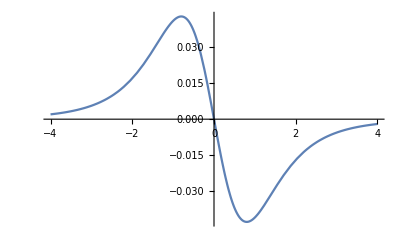

```mathematica
Plot[-((ϵ σ^6 (4 L r δ (15 L^18 (32 r^6 δ^6-21 σ^6)+20 L^16 (-27 z0^2+29 r^2 δ^2) (32 r^6 δ^6-21 σ^6)+64 L^14 (4320 r^6 z0^4 δ^6-7040 r^8 z0^2 δ^8+4960 r^10 δ^10-2835 z0^4 σ^6+4620 r^2 z0^2 δ^2 σ^6-3297 r^4 δ^4 σ^6)+81920 L^6 (-480 r^14 z0^4 δ^14+1664 r^16 z0^2 δ^16+2912 r^18 δ^18-1323 z0^12 σ^6-1764 r^2 z0^10 δ^2 σ^6+273 r^4 z0^8 δ^4 σ^6+r^12 δ^12 (256 z0^6-2413 σ^6)+4 r^10 z0^2 δ^10 (40 z0^6-739 σ^6)+144 r^6 z0^6 δ^6 (14 z0^6-σ^6)+3 r^8 z0^4 δ^8 (896 z0^6+45 σ^6))+1280 L^12 (3360 r^8 z0^4 δ^8-3680 r^10 z0^2 δ^10+2464 r^12 δ^12+1323 z0^6 σ^6-2205 r^2 z0^4 δ^2 σ^6+2373 r^4 z0^2 δ^4 σ^6-9 r^6 δ^6 (224 z0^6+187 σ^6))+1310720 (z0^2+r^2 δ^2)^4 (-192 r^12 z0^4 δ^12+288 r^14 z0^2 δ^14+160 r^16 δ^16+63 z0^10 σ^6+315 r^2 z0^8 δ^2 σ^6+630 r^4 z0^6 δ^4 σ^6+15 r^8 z0^2 δ^8 (-32 z0^6+21 σ^6)+6 r^6 z0^4 δ^6 (-16 z0^6+105 σ^6)-r^10 δ^10 (704 z0^6+193 σ^6))+10240 L^8 (2880 r^12 z0^4 δ^12-4000 r^14 z0^2 δ^14+8288 r^16 δ^16+3969 z0^10 σ^6-735 r^2 z0^8 δ^2 σ^6+378 r^4 z0^6 δ^4 σ^6-54 r^6 z0^4 δ^6 (112 z0^6+5 σ^6)+35 r^8 z0^2 δ^8 (32 z0^6+7 σ^6)-7 r^10 δ^10 (320 z0^6+901 σ^6))+327680 L^2 (z0^2+r^2 δ^2)^2 (-352 r^14 z0^4 δ^14+2368 r^16 z0^2 δ^16+1376 r^18 δ^18-567 z0^12 σ^6-2226 r^2 z0^10 δ^2 σ^6-2625 r^4 z0^8 δ^4 σ^6+2 r^10 z0^2 δ^10 (1616 z0^6-809 σ^6)+12 r^6 z0^6 δ^6 (72 z0^6+35 σ^6)-r^12 δ^12 (640 z0^6+1439 σ^6)+r^8 z0^4 δ^8 (3392 z0^6+3255 σ^6))+2560 L^10 (8640 r^10 z0^4 δ^10-9216 r^12 z0^2 δ^12+7840 r^14 δ^14-3969 z0^8 σ^6+4704 r^2 z0^6 δ^2 σ^6-5082 r^4 z0^4 δ^4 σ^6+24 r^6 z0^2 δ^6 (252 z0^6+223 σ^6)-r^8 δ^8 (7168 z0^6+5597 σ^6))+65536 L^4 (4320 r^16 z0^4 δ^16+12960 r^18 z0^2 δ^18+6560 r^20 δ^20+2835 z0^14 σ^6+9555 r^2 z0^12 δ^2 σ^6+8547 r^4 z0^10 δ^4 σ^6-35 r^8 z0^6 δ^8 (416 z0^6-27 σ^6)-15 r^6 z0^8 δ^6 (288 z0^6+91 σ^6)-15 r^12 z0^2 δ^12 (96 z0^6+1001 σ^6)-5 r^10 z0^4 δ^10 (2592 z0^6+1171 σ^6)-r^14 δ^14 (800 z0^6+6047 σ^6)))+15 (L^4-8 L^2 (z0^2-r^2 δ^2)+16 (z0^2+r^2 δ^2)^2)^5 (32 r^6 δ^6-21 σ^6) ArcTan[(L-2 z0)/(2 r δ)]+15 (L^4-8 L^2 (z0^2-r^2 δ^2)+16 (z0^2+r^2 δ^2)^2)^5 (32 r^6 δ^6-21 σ^6) ArcTan[(L+2 z0)/(2 r δ)]))/(320 r^9 δ^10 (L^2-4 L z0+4 (z0^2+r^2 δ^2))^5 (L^2+4 L z0+4 (z0^2+r^2 δ^2))^5))/.{r->1,L->1,σ->1,z0->2,ϵ->1},{δ,-4,4}]
```

Below is the same plot as above but using the result of {theta,a,1} and substituting the approximation of 0.25 for a from the paper

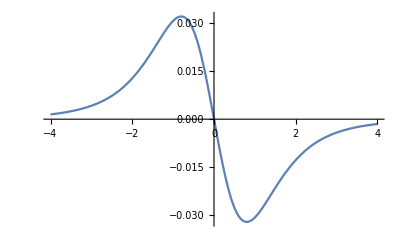

```mathematica
Plot[-4 (-1+a) r^2 δ ϵ σ^6 (1/(1280 r^11 δ^11)((65536 r^9 (L-2 z0) δ^9 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^5)+(18432 r^7 (L-2 z0) δ^7 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^4)+(5376 r^5 (L-2 z0) δ^5 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^3)-(80 r^3 (L-2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^2)-(30 r (L-2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2-4 L z0+4 (z0^2+r^2 δ^2))-15 (32 r^6 δ^6-21 σ^6) ArcTan[(L-2 z0)/(2 r δ)])-1/(1280 r^11 δ^11)(-(65536 r^9 (L+2 z0) δ^9 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^5)-(18432 r^7 (L+2 z0) δ^7 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^4)-(5376 r^5 (L+2 z0) δ^5 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^3)+(80 r^3 (L+2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^2)+(30 r (L+2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2+4 L z0+4 (z0^2+r^2 δ^2))+15 (32 r^6 δ^6-21 σ^6) ArcTan[(L+2 z0)/(2 r δ)]))/.{r->1,L->1,σ->1,z0->2,ϵ->1,a->0.25},{δ,-4,4}]
```

Another attempt to integrate in terms of the remaining variable (lambda) which diverged earlier for -pi to pi. Tried different bounds but it’s taking too long.

```mathematica
Integrate[-4 (-1+a) r^2 δ ϵ σ^6 (1/(1280 r^11 δ^11)((65536 r^9 (L-2 z0) δ^9 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^5)+(18432 r^7 (L-2 z0) δ^7 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^4)+(5376 r^5 (L-2 z0) δ^5 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^3)-(80 r^3 (L-2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^2)-(30 r (L-2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2-4 L z0+4 (z0^2+r^2 δ^2))-15 (32 r^6 δ^6-21 σ^6) ArcTan[(L-2 z0)/(2 r δ)])-1/(1280 r^11 δ^11)(-(65536 r^9 (L+2 z0) δ^9 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^5)-(18432 r^7 (L+2 z0) δ^7 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^4)-(5376 r^5 (L+2 z0) δ^5 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^3)+(80 r^3 (L+2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^2)+(30 r (L+2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2+4 L z0+4 (z0^2+r^2 δ^2))+15 (32 r^6 δ^6-21 σ^6) ArcTan[(L+2 z0)/(2 r δ)]))/.{r->1,L->1,σ->1,z0->2,ϵ->1,a->0.25},{δ,-4,-1}]
```

$Aborted

The above plots were assuming that the -pi,pi bounds are for lambda. But if they are for theta, below is the integral. This was attempted in the first integral which didn’t work so here is the same integral without theta, but it still doesn’t run.

```mathematica
Integrate[r^2 δ (-(4 ϵ σ^6)/(((z-z0)^2+r^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+r^2 δ^2)^6)),{δ,.25,1},{z,-(L/2),(L/2)}]
```

Now below is the same thing but without lambda bounds, only with theta bounds. It gives a result.

```mathematica
Integrate[r^2 δ (-(4 ϵ σ^6)/(((z-z0)^2+r^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+r^2 δ^2)^6)),{z,-(L/2),(L/2)},{θ,-pi,pi}]
```

ConditionalExpression[8 pi r^2 δ ϵ σ^6 (1/(1280 r^11 δ^11)((65536 r^9 (L-2 z0) δ^9 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^5)+(18432 r^7 (L-2 z0) δ^7 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^4)+(5376 r^5 (L-2 z0) δ^5 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^3)-(80 r^3 (L-2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^2)-(30 r (L-2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2-4 L z0+4 (z0^2+r^2 δ^2))-15 (32 r^6 δ^6-21 σ^6) ArcTan[(L-2 z0)/(2 r δ)])-1/(1280 r^11 δ^11)(-(65536 r^9 (L+2 z0) δ^9 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^5)-(18432 r^7 (L+2 z0) δ^7 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^4)-(5376 r^5 (L+2 z0) δ^5 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^3)+(80 r^3 (L+2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^2)+(30 r (L+2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2+4 L z0+4 (z0^2+r^2 δ^2))+15 (32 r^6 δ^6-21 σ^6) ArcTan[(L+2 z0)/(2 r δ)])), ]

Below is a plotting attempt for the above result but nothing shows up.

```mathematica
Plot[8 pi r^2 δ ϵ σ^6 (1/(1280 r^11 δ^11)((65536 r^9 (L-2 z0) δ^9 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^5)+(18432 r^7 (L-2 z0) δ^7 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^4)+(5376 r^5 (L-2 z0) δ^5 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^3)-(80 r^3 (L-2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^2)-(30 r (L-2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2-4 L z0+4 (z0^2+r^2 δ^2))-15 (32 r^6 δ^6-21 σ^6) ArcTan[(L-2 z0)/(2 r δ)])-1/(1280 r^11 δ^11)(-(65536 r^9 (L+2 z0) δ^9 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^5)-(18432 r^7 (L+2 z0) δ^7 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^4)-(5376 r^5 (L+2 z0) δ^5 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^3)+(80 r^3 (L+2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^2)+(30 r (L+2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2+4 L z0+4 (z0^2+r^2 δ^2))+15 (32 r^6 δ^6-21 σ^6) ArcTan[(L+2 z0)/(2 r δ)]))/.{r->1,L->1,σ->1,z0->2,ϵ->1,a->0.25},{δ,-10,10}]
```

-Graphics-

For the attempt to plot above, this is the symbolic result after substitution in case I need it later.

```mathematica
8 pi r^2 δ ϵ σ^6 (1/(1280 r^11 δ^11)((65536 r^9 (L-2 z0) δ^9 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^5)+(18432 r^7 (L-2 z0) δ^7 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^4)+(5376 r^5 (L-2 z0) δ^5 σ^6)/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^3)-(80 r^3 (L-2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2-4 L z0+4 (z0^2+r^2 δ^2))^2)-(30 r (L-2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2-4 L z0+4 (z0^2+r^2 δ^2))-15 (32 r^6 δ^6-21 σ^6) ArcTan[(L-2 z0)/(2 r δ)])-1/(1280 r^11 δ^11)(-(65536 r^9 (L+2 z0) δ^9 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^5)-(18432 r^7 (L+2 z0) δ^7 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^4)-(5376 r^5 (L+2 z0) δ^5 σ^6)/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^3)+(80 r^3 (L+2 z0) δ^3 (32 r^6 δ^6-21 σ^6))/((L^2+4 L z0+4 (z0^2+r^2 δ^2))^2)+(30 r (L+2 z0) δ (32 r^6 δ^6-21 σ^6))/(L^2+4 L z0+4 (z0^2+r^2 δ^2))+15 (32 r^6 δ^6-21 σ^6) ArcTan[(L+2 z0)/(2 r δ)]))/.{r->1,L->1,σ->1,z0->2,ϵ->1,a->0.25}
```

8 pi δ (1/(1280 δ^11)(-(196608 δ^9)/((-7+4 (4+δ^2))^5)-(55296 δ^7)/((-7+4 (4+δ^2))^4)-(16128 δ^5)/((-7+4 (4+δ^2))^3)+(240 δ^3 (-21+32 δ^6))/((-7+4 (4+δ^2))^2)+(90 δ (-21+32 δ^6))/(-7+4 (4+δ^2))+15 (-21+32 δ^6) ArcTan[3/(2 δ)])-1/(1280 δ^11)(-(327680 δ^9)/((9+4 (4+δ^2))^5)-(92160 δ^7)/((9+4 (4+δ^2))^4)-(26880 δ^5)/((9+4 (4+δ^2))^3)+(400 δ^3 (-21+32 δ^6))/((9+4 (4+δ^2))^2)+(150 δ (-21+32 δ^6))/(9+4 (4+δ^2))+15 (-21+32 δ^6) ArcTan[5/(2 δ)]))

We are returning to using {theta,a,1} where a=0.25, but I am subbing the equation for r before integrating to get the symbolic result that will be plotted. Unfortunately it was running for way too long, had to abort.

```mathematica
r^2 δ (-(4 ϵ σ^6)/(((z-z0)^2+r^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+r^2 δ^2)^6))/.{r->r0+4(r1−r0)((z/L)^2)}
```

(r0+(4 (-r0+r1) z^2)/L^2)^2 δ (-(4 ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^6))

```mathematica
Integrate[(r0+(4 (-r0+r1) z^2)/L^2)^2 δ (-(4 ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^6)),{z,-(L/2),(L/2)},{θ,a,1}]
```

$Aborted

## An attempt to graph a cylinder before even graphing the parametric channel itself but doesn’t work

```mathematica
ParametricPlot3D[{rcos[θ],rcos[θ],z},{r,0,1},{θ,0,1},{z,0,1}]
```

ParametricPlot3D::nonopt: Options expected (instead of {z,0,1}) beyond position 3 in ParametricPlot3D[{rcos[θ],rcos[θ],z},{r,0,1},{θ,0,1},{z,0,1}]. An option must be a rule or a list of rules.

ParametricPlot3D[{rcos[θ],rcos[θ],z},{r,0,1},{θ,0,1},{z,0,1}]